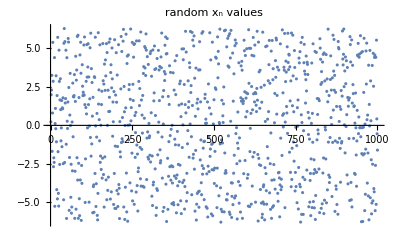

```mathematica
On[Assert]
n = 1000;
testdata = RandomReal[{-2*π, 2*π}, n];

noisify[data_] := data + (.5 * Normal[
RandomFunction[
WhiteNoiseProcess[], 
{0,Dimensions[data][[1]]-1}]][[1]][[All,2]] );

trainingfunction[x_] := noisify[Sin[x]] ;

ListPlot[testdata, PlotLabel->"random x_n values"]
```

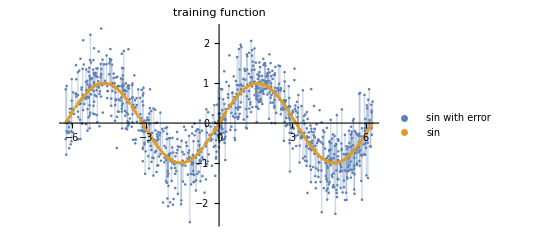

```mathematica
y = Evaluate[trainingfunction[testdata]];
yclean = Evaluate[Sin[testdata]];
plotdata = Transpose@{testdata,y};
plotdataclean = Transpose@{testdata, yclean};
ListPlot[{plotdata, plotdataclean}, PlotLabel->"training function (with random error)",  Filling->{1 -> {2}}, PlotLegends-> Placed[{"sin with error", "sin"}, Right]]
```